```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import["../mathematica/lib/util.m"]
```

```mathematica
data1 =Import["../runs/Trials/16979417/19638077.dat","Table"];
d1p = Import["D:\\GitHub\\Black-Hole-Project\\ccode\\matrix-models-cpp\\runs\\Trials\\16979417\\27541016.dat","Table"];
```

```mathematica
data2 =Import["..\\runs\\Trials\\17122745\\29425012.dat","Table"];
```

```mathematica
data3 = Import["D:\\GitHub\\Black-Hole-Project\\ccode\\matrix-models-cpp\\runs\\Trials\\22375915\\11448461.dat","Table"];
```

```mathematica
data4 = Import["D:\\GitHub\\Black-Hole-Project\\ccode\\matrix-models-cpp\\runs\\Trials\\23308331\\10663337.dat","Table"];
```

```mathematica
Dimensions[data1]
```

{10000,379}

```mathematica
ms ={ Map[radius,data1],Map[radius,data2],Map[radius,data3]};
```

```mathematica
ListLogPlot[ms[[1;;1000,2]]]
SmoothHistogram[ms[[All, 2]]]
```

```mathematica
d1 = SmoothKernelDistribution[ms[[1,All,2]]];
d2= SmoothKernelDistribution[ms[[2,All,2]]];
d3= SmoothKernelDistribution[ms[[3,All,2]]];
```

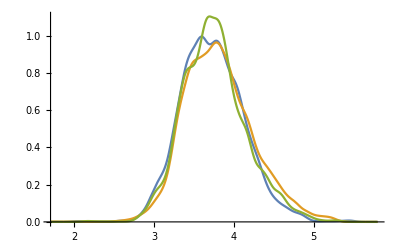

```mathematica
Plot[{PDF[d1][x],PDF[d2][x],PDF[d3][x]},{x,1.7,5.8}]
```

```mathematica
msp = Map[radius,d1p];
d1p = SmoothKernelDistribution[msp[[All,2]]];
```

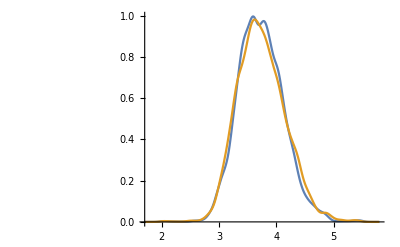

```mathematica
Plot[{PDF[d1][x],PDF[d1p][x]},{x,1.7,5.8}]
```

```mathematica
Mean[d1p]
```

3.74071

```mathematica
StandardDeviation[d1p]
```

0.420932

```mathematica
Mean[d1p]/StandardDeviation[d1p]
```